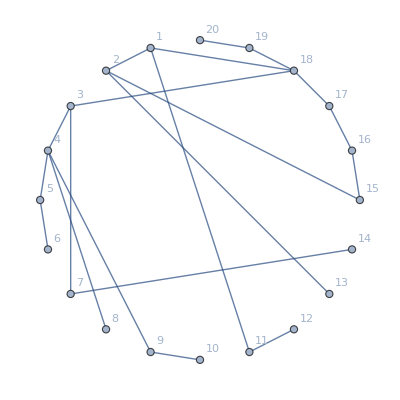
{{-Graphics-},3.65789}

{139/38}

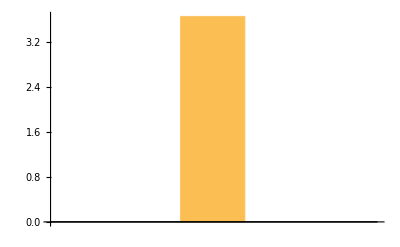

```mathematica
aplMin=50000;
mMin;
dataGraph={};
r=10;
(*----------Basic Setup----------*)
(*For[r=1,r<11,r++,*)
For[var=1,var<100,var++,
n=20;

(*----------Distance Matrice between the nodes----------*)
m=IncidenceMatrix[CycleGraph[n]];
(*---m[[2,3]]=0; m[[7,3]]=1;---*)
(*----------Rewireing----------*)
(*-----m[[coloumn,row]]-----*)
outputString={{(*old*)},{(*new*)}};
Label[begin];
Do[
mjEdge=Random[Integer,{1,n}];
For[j=1,j<n+1,j++,
If[m[[j,mjEdge]]==1 && j≠mjEdge ,
miOld=j;
];
];
Label[againRandom];
miNew=Random[Integer,{1,n}];
If[miNew == mjEdge || miNew==miOld,Goto[againRandom],Goto[check]];
Label[check];


Label[done];
AppendTo[outputString[[1]],{miOld,mjEdge}];
AppendTo[outputString[[2]],{miNew,mjEdge}];
m[[miOld,mjEdge]]=0;
m[[miNew,mjEdge]]=1;
,r];

(*----------------------------*)
Grid[outputString,Frame->{All,None}];


matrixLabel=Table[x,{x,n}];
(*Print[MatrixForm[m, TableHeadings->{matrixLabel,matrixLabel}]];*)

Check[IncidenceGraph[m,VertexLabels->"Name",EdgeLabels->"Name"];,Goto[begin]];
m=IncidenceGraph[m];
(*Print[Table[Graph[m,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}]];*)

(*----------Average Path Length Calculation----------*)


(*----------Output----------*)
apl=MeanGraphDistance[m];
(*Print[N[apl]];*)

If[apl≠ ∞,
If[apl<aplMin,
aplMin=apl;
mMin=m;
];
];
];

Print[{Table[Graph[mMin,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}],N[aplMin]}];
AppendTo[dataGraph,aplMin];
aplMin=50000;
(*]*)
Print[dataGraph];
Show[BarChart[dataGraph]]
```